```mathematica
Clear[ic,i,iph1,iph,tau,t,r,c,x,k,t];
```

```mathematica
iph[t_/;0≤t≤tau]:=k*t;
iph[t_/;tau≤t≤2*tau]:=k*tau-k(t-tau);
iph[t_/;2*tau≤t≤10*tau]:=0;
iph[t_/;10*tau<t<=100*tau]:=iph[Mod[t,10*tau]];
```

```mathematica
tau=2×10^-9;k=10000;
```

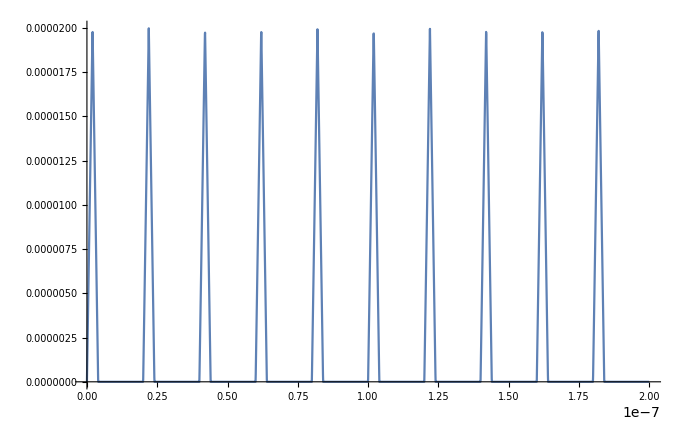

```mathematica
Plot[iph[t], {t,0,100*tau},PlotRange->Full]
```

```mathematica
sol=NDSolve[{(i[t]-iph[t])/c+i'[t]*r==0,PeriodicBoundaryCondition[i[t],t==0,TranslationTransform[{10*tau}]]},i,{t,0,20*tau}]/.{c->5 10^-12,r->500}
```

NDSolve::femcnmd: The PDE coefficient {{r}} does not evaluate to a numeric matrix of dimensions {1,1} at the coordinate {2.×10^-8}.

NDSolve::femcscd: The PDE is convection dominated and the result may not be stable. Adding artificial diffusion may help.

NDSolve::femibcnd: No DirichletCondition or Robin-type NeumannValue was specified for {i}; the result is not unique up to a constant.

{{i→                                 -8
InterpolatingFunction[{{0., 4. 10  }}, <>]}}

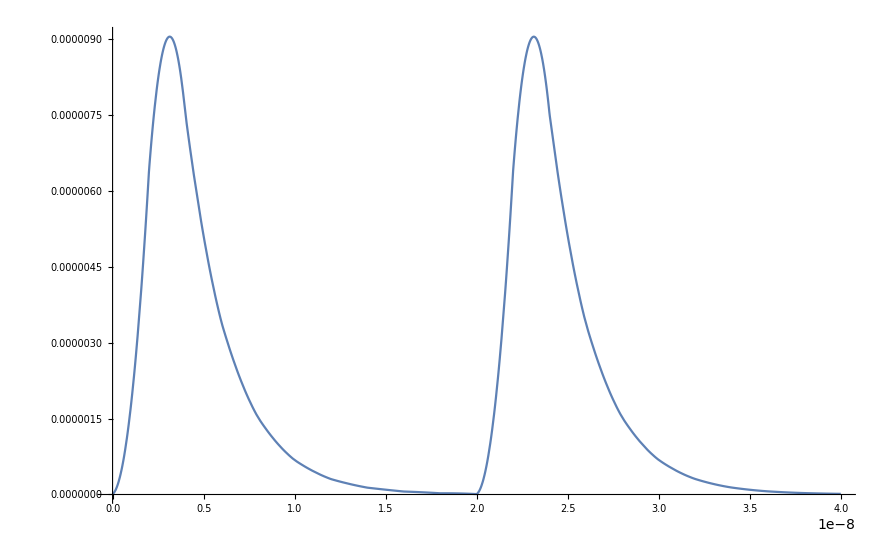

```mathematica
Plot[i[t]/.sol/.{tau->2×10^-9,k->10000,c->5 10^-12,r->500},{t,0,40*tau},PlotRange->All]
```